MedaChem, Inc.
1219 Broad St.
Durham, NC 27705

May 20, 2021
To: Vertextin
From: Aakriti Lakshmanan & Riya Kabra
Subj: Antiviral Drug Analysis

## Abstract

In this paper, we describe the pharmacokinetic and pharmacodynamic parameters of four antivirals that have had increased usage throughout the Covid-19 pandemic: Oseltamivir, Zanamivir, Peramivir, and Laninamivir. This is accomplished by analyzing a variety of these drugs’ characteristics through ADME studies, PK modeling, Torch 3D studies, and more.

## Pharmacokinetics

## 2.1. ADME Studies

### 2.1.1. Drug Structural Profiles

Below, the structural profiles of each of the four drugs is provided.

```mathematica
peramivirStructure = Import["C:\\Users\\Riya Kabra\\Desktop\\Computational Medicinal Chemistry\\peramivir structure.jpg"];
inavirStructure = Import["C:\\Users\\Riya Kabra\\Desktop\\Computational Medicinal Chemistry\\laninamivir structure.jpg"];
```

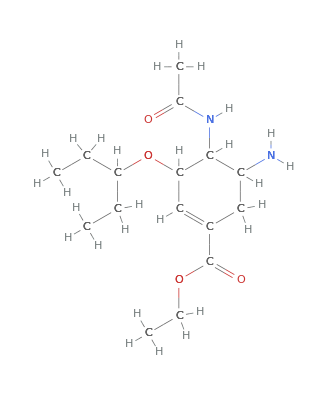
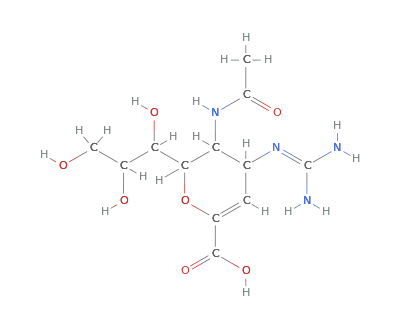
Name | Brand Name | IUPAC Name | Structural Formula | Functional Groups
Oseltamivir | Tamiflu | ethyl (3R,4R,5S)-4-acetamido-5-amino-3-pentan-3-yloxycyclohexene-1-carboxylate | -Graphics- | alkane, alkene, ester, ether, primary amine, amide
Zanamivir | Relenza | (4S,5R,6R)-5-acetamido-4-(diaminomethylideneamino)-6-[(1R,2R)-1,2,3-trihydroxypropyl]-5,6-dihydro-4H-pyran-2-carboxylic acid | -Graphics- | alkane, alkene, amide, alcohol, ether, carboxylic acid, primary amine, secondary amine
Peramivir | Rapivab | (1S,2S,3R,4R)-4-carbamimidamido-3-[(1S)-1-acetamido-2-ethylbutyl]-2-hydroxycyclopentane-1-carboxylic acid | -Graphics- | alkane, carboxylic acid, alcohol, amide, primary amine, secondary amine
Laninamivir | Inavir | (2R,3R,4S)-4-carbamimidamido-2-[(1R,2R)-2,3-dihydroxy-1-methoxypropyl]-3-acetamido-3,4-dihydro-2H-pyran-6-carboxylic acid | -Graphics- | alkane, alkene, amide, carboxylic acid, alcohol, ether, primary amine, secondary amine

```mathematica
Grid[{{"Name", "Brand Name", "IUPAC Name", "Structural Formula", "Functional Groups"}, {"Oseltamivir", "Tamiflu", ChemicalData["Oseltamivir","IUPACName"], ChemicalData["Oseltamivir","CHColorStructureDiagram"], "alkane, alkene, ester, ether, primary amine, amide"}, {"Zanamivir", "Relenza", ChemicalData["Zanamivir","IUPACName"], ChemicalData["Zanamivir","CHColorStructureDiagram"], "alkane, alkene, amide, alcohol, ether, carboxylic acid, primary amine, secondary amine"}, {"Peramivir", "Rapivab", "(1S,2S,3R,4R)-4-carbamimidamido-3-[(1S)-1-acetamido-2-ethylbutyl]-2-hydroxycyclopentane-1-carboxylic acid", peramivirStructure, "alkane, carboxylic acid, alcohol, amide, primary amine, secondary amine"}, {"Laninamivir", "Inavir", "(2R,3R,4S)-4-carbamimidamido-2-[(1R,2R)-2,3-dihydroxy-1-methoxypropyl]-3-acetamido-3,4-dihydro-2H-pyran-6-carboxylic acid", inavirStructure, "alkane, alkene, amide, carboxylic acid, alcohol, ether, primary amine, secondary amine"}},ItemStyle -> {0 -> Bold, 1-> Bold}, Frame -> All]
```

*Note: For data that was not available on Mathematica, DrugBank was used to find additional information.

### 2.1.2. StarDrop ADME(T) Studies

In this section, we conduct ADME(T) studies for each of the four drugs.

Data Importation

In order to import the drug data into StarDrop, a .csv file of the compound name and SMILES formula was created as shown below.

```mathematica
antiviralsFile=Import["C:\\Users\\Riya Kabra\\Desktop\\Computational Medicinal Chemistry\\final project antivirals.csv"];
Grid[antiviralsFile,ItemStyle -> {0 -> Bold, 1-> Bold},  Frame -> All]
```

Compound Name | SMILES | 
Oseltamivir | CCOC(=O)C1=CC(OC(CC)CC)C(NC(C)=O)C(N)C1 | 
Zanamivir | CC(=O)NC1C(C=C(OC1C(C(CO)O)O)C(=O)O)N=C(N)N | 
Peramivir | [H][C@@]1([C@@H](NC(C)=O)C(CC)CC)[C@H](O)[C@H](C[C@H]1NC(N)=N)C(O)=O | 
Laninamivir | [H][C@]1(OC(=C[C@H](NC(N)=N)[C@H]1NC(C)=O)C(O)=O)[C@H](OC)[C@H](O)CO |

Results

Using StarDrop models, we were able to produce the following ADME parameters for each compound.

```mathematica
stardropAntivirals=Import["C:\\Users\\Riya Kabra\\Desktop\\Computational Medicinal Chemistry\\final project stardrop parameters.csv"];
Grid[stardropAntivirals,ItemStyle -> {0 -> Bold, 1-> Bold},  Frame -> All]
```

Compound Name | SMILES | logS | logP | 2C9 pKi | MW | HBA | HBD | TPSA | Rotatable Bonds | Oral Rat -log(LD50) M/kg | QED_ALERTS | Lipinski Rule of Five_Score | Oral CNS Scoring Profile_Score | Intravenous CNS Scoring Profile_Score
Oseltamivir | CCOC(=O)C1=CC(OC(CC)CC)C(NC(C)=O)C(N)C1 | 3.704 | 1.767 | 4.263 | 312.4 | 6 | 2 | 90.65 | 9 | 2.453 | 1 | 1 | 0.2087 | 0.2207
Zanamivir | CC(=O)NC1C(C=C(OC1C(C(CO)O)O)C(=O)O)N=C(N)N | 5.38 | -2.554 | 4.332 | 332.3 | 11 | 7 | 200.7 | 7 | 1.999 | 2 | 0.25 | 0.05151 | 0.07869
Peramivir | [H][C@@]1([C@@H](NC(C)=O)C(CC)CC)[C@H](O)[C@H](C[C@H]1NC(N)=N)C(O)=O | 3.701 | 0.2213 | 4.259 | 328.4 | 8 | 6 | 148.5 | 9 | 2.281 | 2 | 0.5 | 0.1243 | 0.1593
Laninamivir | [H][C@]1(OC(=C[C@H](NC(N)=N)[C@H]1NC(C)=O)C(O)=O)[C@H](OC)[C@H](O)CO | 5.036 | -2.492 | 4.395 | 346.3 | 11 | 7 | 187.2 | 9 | 2.155 | 2 | 0.25 | 0.04816 | 0.07417

Conclusions

Once we take a look at the structural profile of each drug as provided above, we can predict the drug’s effectiveness by utilizing information from specific attributes. We use Lipinski’s rules to provide general guidelines on how well a drug may perform, although those rules should not be used as hard cutoffs for any drugs.

Pharmacokinetic Parameters

Partition Coefficient (logP): This describes the lipophilicity or hydrophobicity of a compound. It provides evidence regarding the penetration of a drug through the membrane of a cell or tissue. Lipinski indicates that oral drugs have a logP value <5, which all of the drugs above follow.

2C9 pKi: This is the binding affinity of a drug, which explains the ability of the drug to bind to the Cytochrome P450 2C9 protein in the body. All of these drugs have a pKi value that is less than 6, which falls under low to medium binding affinity.

Molecular Weight: As per Lipinksi’s rules, oral drugs should have a molar mass less than 500 g/mol. All of the drugs above follow this rule.

Hydrogen Bond Acceptors/Donors: Bonding properties enable medicinal chemists to explore how drugs interact with molecules in the human body. The aim is for a drug to have <5 hydrogen bond donors and <10 hydrogen bond acceptors. Oseltamivir follows both of these Lipinski guidelines, and Peramivir has an acceptable number of HBAs. However, it does not follow the HBD guideline, and Zanamivir and Laninamivir follow neither guideline.

Topological Polar Surface Area: Studying the TPSA of a drug (in square angstroms) shows whether a drug has the ability to penetrate a membrane based on its polarity. Lipinski’s Rules state that a suitable drug TPSA is <140 angstroms. Once again, Oseltamivir follows this guideline and Peramivir has a TPSA just above 140 Angstroms, but Zanamivir and Laninamivir fail to match this property rule.

Rotatable Bonds: It is beneficial for drugs to have less than 10 rotatable bonds so that they do not change configurations in the body significantly, as per Lipinski’s rules. All drugs above abide by this rule.

Additional Models

Oral Rat Toxicity Model -- These values (ranging around two mols/kg for these antivirals) indicate the toxicity of a substance for an individual. For example, a 100 kg individual can determine that about 100*2 = 200 molar of the drug is toxic for them.

QED Alerts Analysis -- The StarDrop team and Matt Segall have provided this metric to determine how successful a drug may be. Similarly to Lipinski’s Rule of Five, the QED Alerts analysis utilizes eight specific properties and weights some qualities higher based on if they are more vital to the success of a drug (such as PSA or MW). The result of this analysis indicates the number of red flags for the drug based on the calculated metric. Three out of the four drugs have two red flags, while Oseltamivir has one red flag.

Lipinski’s Rule of Five Model -- This scoring profile utilizes one metric to determine how well a drug follows Lipinski’s Rule of Five guidelines. The score ranges from 0-1, and the higher a drug’s score, the more suitable a drug is to be provided orally. Oseltamivir is exactly 1, indicating it will be a successful oral drug. However, the other three drugs are significantly less ideal with metrics around 0.25-0.50.

Oral CNS & Intravenous CNS Scoring Profiles: All of these drugs have very low scores for both of these profiles; Oseltamivir is in the lead with a score of ~0.2, Paramivir following with ~0.1, and Zanamivir and Laninamivir with scores close to 0 for both of these profiles. Based on their scores, these drugs are not designed to be given as IV drugs or as oral drugs that affect the central nervous system and cross the blood brain barrier. This would make sense, given that these are antivirals that are not meant to be taken as CNS drugs.

### 2.1.3. Solubility Analysis

Qualitative Measurements

Empirical Method

We can use Lemke’s empirical methods to estimate the solubility of a compound. The guidelines to estimating are given in the chart below:

Functional Group | Mono-functional Compound | Poly-functional compound
Alcohol | 5-6 carbons | 3-4 carbons
Phenol | 6-7 carbons | 3-4 carbons
Ether | 4-5 carbons | 2 carbons
Aldehyde | 4-5 carbons | 2 carbons
Ketone | 5-6 carbons | 2 carbons
Amine | 6-7 carbons | 3 carbons
Carboxylic acid | 5-6 carbons | 3 carbons
Ester | 6 carbons | 3 carbons
Amide | 6 carbons | 2-3 carbons

We will predict solubility using the guidelines in the chart below:

```mathematica
Grid[{{"Ratio of soluble carbons/total carbons", "Compound"}, {"<50%", "Not soluble"}, {"50-75%", "Slightly Soluble"}, {">75%", "Soluble"}}, ItemStyle -> {0 -> Bold, 1-> Bold},  Frame -> All]
```

Ratio of soluble carbons/total carbons | Compound
<50% | Not soluble
50-75% | Slightly Soluble
>75% | Soluble

Finally, we produce the qualitative solubility chart below:

```mathematica
Grid[{{"Compound", "Qualitative Solubility"}, {"Oseltamivir", "Slightly soluble"}, {"Zanamivir", "Soluble"}, {"Peramivir", "Soluble"}, {"Laninamivir", "Soluble"}}, ItemStyle -> {0 -> Bold, 1-> Bold},  Frame -> All]
```

Compound | Qualitative Solubility
Oseltamivir | Slightly soluble
Zanamivir | Soluble
Peramivir | Soluble
Laninamivir | Soluble

Quantitative Measurements

General Solubility Equation

The General Solubility Equation is a method used to predict the logS of a compound using specific parameters. It is listed below:

logS = 0.8 - logP - 0.01(MP-25)

Data Importation

Using the data below (*values compiled from different sources), we can calculate the logS for each of the four compounds.

```mathematica
myData=Import["C:\\Users\\Riya Kabra\\Desktop\\Computational Medicinal Chemistry\\general solubility data.csv"];table = Grid[myData,ItemStyle -> {0 -> Bold, 1-> Bold},Frame -> All]
```

Compound | logP | MP
Oseltamivir | 1.767 | 206
Zanamivir | -2.554 | 256
Peramivir | 0.2213 | 260
Laninamivir | -2.492 | 300

Results

Shown above is the calculated logS value for each antiviral. These values may differ from logS values provided in other databases such as StarDrop as the initial values may be different and the General Solubility Equation model is an estimate.

```mathematica
dataNoLabels = Delete[myData, 1];
{name, logp, mp} = Transpose[dataNoLabels];
myFunction[logp_, mp_]:=0.8 - logp - 0.01*(mp-25)
solubility = myFunction[logp, mp];
finalsolubilitydata = Transpose[{name, solubility}];
table = Prepend[finalsolubilitydata, {"Name","Solubility"}];
Grid[table,ItemStyle -> {0 -> Bold, 1-> Bold}, Frame -> All]
```

Name | Solubility
Oseltamivir | -2.777
Zanamivir | 1.044
Peramivir | -1.7713
Laninamivir | 0.542

Abraham Solvation Parameters

As described in Chapter 4 (Gotwals, Introduction to Medicinal Chemistry), Stanley Abraham developed an equation to predict the logBB value, a measure of how well a drug crosses the blood - brain barrier. The equation is shown below:

logBB= 0.044 + 0.511E - 0.886 S - 0.724 A -0.666 B + 0.861 V

Plugging in the solvation parameters provided by the Vertextin manager into the equation, we can predict the logBB solubility value. Below are the calculated solvation parameters:

A: 0.5
B: 1.87
Bo: 1.88
L: 10.911
S: 2.07
E: 0.94
V: 2.5598

```mathematica
myFunction[es_,s_,a_,b_,v_]:=0.044+0.511es-0.886s-0.724a-0.666b+0.861v
logbb = myFunction[0.94, 2.07, 0.5, 1.87, 2.5598];
Print["The logBB value is ", logbb, " for Oseltamivir."]
```

The logBB value is -0.713112 for Oseltamivir.

## 2.2. PK Modeling

Using a pharmacokinetic model, the dosage regimen for oseltamivir for a set of individuals at different weights was determined. Oseltamivir oral capsules come in sizes of 30 mg, 45 mg and 75 mg. The drug is also provided in the form of an oral suspension, but for the consideration of the model below, only the capsule form is taken into account. 11 different patients were examined, ranging from a weight of 10 - 110 kg. This range was chosen since it would accurately span the weights of the majority of individuals, providing a comprehensive source for dosage regimens. The dosing regimens for these individuals is summarized in the table below. Individuals who weigh less than 10 kg, which are not mentioned in the below graph, should only take one 30 mg capsule every 24 hours. Dosages or intervals higher than those mentioned may lead to plasma drug concentrations above the LD50, which can be harmful to the body. 

Patient Weight (kg) | Size of Pill (mg) | Number of Pills | Interval (hrs) | Concentration Graph
10 | 30 | 1 | 6 | -Graphics-
20 | 30 | 2 | 6 | -Graphics-
30 | 45 | 2 | 6 | -Graphics-
40 | 75 | 2 | 8 | -Graphics-
50 | 45 | 4 | 8 | -Graphics-
60 | 75 | 3 | 8 | -Graphics-
70 | 45 | 6 | 8 | -Graphics-
80 | 75 | 4 | 8 | -Graphics-
90 | 75 | 5 | 8 | -Graphics-
100 | 75 | 5 | 8 | -Graphics-
110 | 75 | 6 | 8 | -Graphics-

## 2.3. Liver Flow Modeling

Oseltamivir is mainly metabolized in the liver. Therefore, understanding the liver blood flow values is important because it can help inform dosage regimens as seen above.  The following table summarizes the given liver blood flow data form external animal model studies.

```mathematica
animal = {"Mouse","Rat","Rabbit", "Monkey","Dog"};
weight = {0.02,0.25, 2.5, 5.0,10.0};
liverflow = {1.8,13.8,177,218,309};
liverdataall= Transpose[{animal,weight,liverflow}];
liverdataall = Insert[liverdataall,{"Animal","Weight(kg)","Hepatic blood flow (mL/min)"},1];
Grid[liverdataall,ItemStyle -> {0 -> Bold, 1-> Bold},  Frame -> All]
```

Animal | Weight(kg) | Hepatic blood flow (mL/min)
Mouse | 0.02 | 1.8
Rat | 0.25 | 13.8
Rabbit | 2.5 | 177
Monkey | 5. | 218
Dog | 10. | 309

Using this data, we have built a regression model with an R^2 value of .88 to predict the liver blood flow value for humans. Given that humans weigh 70 kg on average, the estimated liver blood flow is 2160.48 mL/min.

```mathematica
liverdatajoint = Transpose[{weight,liverflow}];
liverFit =LinearModelFit[liverdatajoint, {weightX},{weightX}];
livernonlinearfit = NonlinearModelFit[liverdatajoint, a weightY^2 + b weightY + c, {a,b,c}, weightY];
Print["Linear Regression Model: Hepatic Blood Flow = ", TraditionalForm[Normal[liverFit]]]
Print["Linear Regression Model R Squared Value: ", liverFit["RSquared"]]
Print["Human Hepatic Blood Flow Estimate: ", liverFit[70], " mL/min."]
```

Linear Regression Model: Hepatic Blood Flow = 30.3489 weightX+36.0601

Linear Regression Model R Squared Value: 0.884653

Human Hepatic Blood Flow Estimate: 2160.48 mL/min.

## 2.4. Metabolism Studies

Provided below are the results of the metabolism studies on each of the four antivirals using the P450 server on StarDrop. Each antiviral was analyzed to track which of the CYP enzymes metabolized and affected the drug in the body.

```mathematica
myData=Import["C:\\Users\\Riya Kabra\\Desktop\\Computational Medicinal Chemistry\\final project metabolism studies.csv"];table = Grid[myData,ItemStyle -> {0 -> Bold, 1-> Bold},Frame -> All]
```

Compound Name | SMILES | P450 Isoform | P450_3A4_CSL | P450_3A4_Labile | P450_3A4_Mod_Labile | P450_3A4_Mod_Stable | P450_3A4_Stable
Oseltamivir | CCOC(=O)C1=CC(OC(CC)CC)C(NC(C)=O)C(N)C1 | 3A4 | 0.6317 | 0 | 1 | 5 | 8
Zanamivir | CC(=O)NC1C(C=C(OC1C(C(CO)O)O)C(=O)O)N=C(N)N | 3A4 | 0.9653 | 2 | 2 | 0 | 7
Peramivir | [H][C@@]1([C@@H](NC(C)=O)C(CC)CC)[C@H](O)[C@H](C[C@H]1NC(N)=N)C(O)=O | 3A4 | 0.9022 | 1 | 0 | 0 | 13
Laninamivir | [H][C@]1(OC(=C[C@H](NC(N)=N)[C@H]1NC(C)=O)C(O)=O)[C@H](OC)[C@H](O)CO | 3A4 | 0.925 | 1 | 0 | 2 | 8

As portrayed above, each drug is primarily metabolized by the CYP34A enzyme. A more detailed process of each drug’s biochemical pathway in the body can be found on the database PharmGKB.

The CSL (Composite Site Lability) value portrays how much the drug is being metabolized in the body. The goal is to have the smallest CSL possible (unless we are dealing with a prodrug) in order to keep it concentrated in the bloodstream for longer periods of time rather than being metabolized quickly. The initial CSL values are close to 1, or quite high for all of the drugs, although Oseltamivir is closer to the objective of 0 with a score of 0.63. The way to bring down the CNL score is to create an analog of each drug and apply transformations to its labile sites. Some transformations include adding substituents to increase the steric hindrance of a compound, but a medicinal chemist has to ensure that these types of transformations don’t alter the therapeutic effect of the drug as well. 

The number of labile (unstable), moderately labile, moderately stable, and stable sites are provided in the data table above. The positions of these sites can also be visualized using P450 graphics, in which the ratios indicate the amount that each site is metabolized by the CYP34A enzyme:

Oseltamivir

```mathematica
Import["C:\\Users\\Riya Kabra\\Desktop\\Computational Medicinal Chemistry\\oseltamivir p450.jpg"]
```

-Graphics-

Zanamivir

```mathematica
Import["C:\\Users\\Riya Kabra\\Desktop\\Computational Medicinal Chemistry\\zanamivir p450.jpg"]
```

-Graphics-

Peramivir

```mathematica
Import["C:\\Users\\Riya Kabra\\Desktop\\Computational Medicinal Chemistry\\peramivir p450.jpg"]
```

-Graphics-

Laninamivir

```mathematica
Import["C:\\Users\\Riya Kabra\\Desktop\\Computational Medicinal Chemistry\\laninamivir p450.jpg"]
```

-Graphics-

## 2.5. QSAR Studies

In this section, we conduct a QSAR study on oseltamivir using the data provided by the Vertextin manager. The data includes the following properties:

Dipole Moment: how polar each compound is (in Debyes)

Energy: how much energy each compound produces (in electron-volts)

HOMO: how much energy the compound has in occupied molecular orbitals (in electron-volts)

LUMO: the level of energy where electrons go following an energy addition to a compound (in electron-volts)

pIC50: represents the binding affinity of a compound. A higher pIC50 value corresponds to the stronger inhibition of a protein.

Data Importation and Extraction

```mathematica
myData=Import["C:\\Users\\Riya Kabra\\Desktop\\Computational Medicinal Chemistry\\OseltamivirQSARdata.csv"];table = Grid[myData,ItemStyle -> {0 -> Bold, 1-> Bold},Frame -> All]
```

Compound | DM | Energy | HOMO | LUMO | pIC50
1 | 5.968 | -45143.7 | -5.929 | -1.07 | 6.7
2 | 5.959 | -36415.6 | -5.716 | -1.047 | 5.93
3 | 6.288 | -39625.3 | -5.662 | -0.972 | 5.84
4 | 6.446 | -39532. | -5.596 | -1.168 | 6.26
5 | 6.167 | -42703.2 | -5.701 | -1.156 | 6.82
6 | 5.042 | -32267.8 | -5.795 | -1.162 | 6.17
7 | 4.991 | -33337.7 | -5.796 | -1.144 | 6.64
8 | 5.117 | -34407.6 | -5.761 | -1.145 | 6.11
9 | 5.101 | -33337.7 | -5.776 | -1.149 | 5.94
10 | 5.183 | -34407.5 | -5.925 | -1.142 | 6.43
11 | 5.005 | -35477.2 | -5.748 | -1.177 | 6.02
12 | 4.942 | -38555.2 | -5.802 | -1.507 | 6.1
13 | 3.51 | -26079.1 | -6.178 | -1.457 | 7.77
14 | 2.66 | -30128.8 | -5.995 | -1.478 | 8.16
15 | 3.58 | -31428.2 | -5.776 | -1.481 | 7.57
16 | 3.6 | -29288.5 | -5.803 | -1.477 | 7.72
17 | 3.608 | -29288.6 | -5.808 | -1.648 | 7.11
18 | 3.718 | -41094.5 | -5.262 | -1.618 | 7.82
19 | 3.243 | -32366.6 | -5.34 | -1.49 | 8.15
20 | 2.836 | -35482.9 | -5.201 | -1.492 | 7.51
21 | 3.075 | -34413.3 | -5.251 | -1.597 | 7.68
22 | 4.362 | -44872.7 | 5.732 | -1.578 | 8.44
23 | 4.275 | -102330. | -5.688 | -1.613 | 7.89
24 | 4.361 | -35066.8 | -5.507 | -1.681 | 8.
25 | 4.007 | -34472.9 | -4.98 | -1.653 | 7.85
26 | 3.218 | -38654.1 | -5.133 | -1.506 | 8.72
27 | 3.579 | -34506. | -5.855 | -1.426 | 7.5
28 | 2.159 | -41709.7 | -5.056 | -1.481 | 7.23
29 | 2.733 | -37588.9 | -5.19 | -1.609 | 7.05
30 | 4.334 | -51160.2 | -5.561 | -1.572 | 7.96
31 | 3.149 | -44941.6 | -5.31 | -1.673 | 7.37
32 | 3.697 | -47382.3 | -5.086 | -1.107 | 8.68

```mathematica
dataNoLabels = Delete[myData, 1];
{cmpd,dm, energy, homo, lumo, pic50} = Transpose[dataNoLabels];
```

Calculations

Regression Analysis

Dipole Moment

```mathematica
rawData = Transpose[{dm, pic50}]; 
dmPrediction = LinearModelFit[rawData, {x1dipolemoment},{x1dipolemoment}];
```

HOMO LUMO Gap

```mathematica
gap = homo-lumo;
rawData = Transpose[{gap, pic50}];
gapPrediction = LinearModelFit[rawData, {x1gap}, {x1gap}];
```

Energy

```mathematica
rawData = Transpose[{energy, pic50}]; 
energyPrediction = LinearModelFit[rawData, {x1energy},{x1energy}];
```

HOMO

```mathematica
rawData = Transpose[{homo, pic50}]; 
homoPrediction = LinearModelFit[rawData, {x1homo},{x1homo}];
```

LUMO

```mathematica
rawData = Transpose[{lumo, pic50}]; 
lumoPrediction = LinearModelFit[rawData, {x1lumo},{x1lumo}];
```

Best Value

```mathematica
picTarget = Mean[pic50];
dmSolve = NSolve[dmPrediction[x] == picTarget, x];
dmConstant=x/.dmSolve[[1]];
gapSolve  = NSolve[gapPrediction[x] == picTarget, x];
gapConstant=x/.gapSolve[[1]];
energySolve  = NSolve[energyPrediction[x] == picTarget, x];
energyConstant=x/.energySolve[[1]];
homoSolve  = NSolve[homoPrediction[x] == picTarget, x];
homoConstant=x/.homoSolve[[1]];
lumoSolve  = NSolve[lumoPrediction[x] == picTarget, x];
lumoConstant=x/.lumoSolve[[1]];
```

Results

This table provides the results of using specific variables to predict pIC50 values. Their correlation of determinations are also provided, which portrays the amount of variability in the pic50 values that account for variation in the independent variables. In other words, it shows the strength of a linear relationship amongst the two variables. Dipole moment proves to have the strongest association with pic50 values, with LUMO being the second best predictor. Each variable’s value to predict the average pic50 value is also provided in the table.

```mathematica
Grid[{{"Predictor", "Equation", "R^2", "Best Value"}, {"Dipole", Normal[dmPrediction], dmPrediction["RSquared"], dmConstant}, {"Gap", Normal[gapPrediction], gapPrediction["RSquared"], gapConstant}, {"Energy", Normal[energyPrediction], energyPrediction["RSquared"], energyConstant}, {"HOMO", Normal[homoPrediction], homoPrediction["RSquared"], homoConstant}, {"LUMO", Normal[lumoPrediction], lumoPrediction["RSquared"], lumoConstant}}, ItemStyle -> {1-> Bold, 1-> Bold},Frame -> All]
```

Predictor | Equation | R^2 | Best Value
Dipole | 9.39446-0.511229 x1dipolemoment | 0.463531 | 4.24728
Gap | 7.83083+0.15813 x1gap | 0.142318 | -3.84309
Energy | 6.74945-0.0000121508 x1energy | 0.032229 | -38983.3
HOMO | 7.93526+0.136086 x1homo | 0.0995695 | -5.23297
LUMO | 3.6844-2.54607 x1lumo | 0.428604 | -1.38988

Multiple Linear Regression

We can also find the best combination of predictors for pIC50 using multiple linear regression. After testing a number of predictors, the variables dipole moment, HOMO, and LUMO produced one of the highest R^2 values to predict pIC50.

```mathematica
rawData = Transpose[{dm, homo, lumo, pic50}];
pic50Predict = LinearModelFit[rawData, {x1dm, x2homo, x3lumo},{x1dm, x2homo, x3lumo}];
Print["pIC50 activity = ", Normal[pic50Predict]]
Print["R^2 = ", pic50Predict["RSquared"]]
```

pIC50 activity = 7.9619-0.365162 x1dm+0.102937 x2homo-0.971914 x3lumo

R^2 = 0.57002

## Pharmacodynamics

## 3.1. Description of the Neuraminidase Enzyme

Neuraminidase enzymes are a group of enzymes whose primary function is to cut the glycosidic bond, a covalent bond between a carbohydrate and other molecule, in neuraminic acids. Viral neuraminidase uses this function to help a virus be released from the infected host cell. The influenza virus contains two glycoproteins, hemagglutinin and neuraminidase. The function of the hemagglutinin is to help the virus bind to sialic acid groups on the surface of the host cell. However, without the neuraminidase, the virus would be stuck to a specific receptor/sialic acid group which may not be the right one for the virus to get into the cell. Viral neuraminidase solves this issue by cleaving the glycosidic bond between hemagglutinin and the sialic acid groups, allowing the virus to move to other sialic acid groups on the surface of the cell until the correct receptor is found. Neuraminidase, otherwise known as NA, also helps the virus after replication by ensuring that viral particles are not bonded to sialic acid and that self-aggregation does not occur. [1][2] The genome of influenza viruses consists of segmented RNA strands. Strand 6 of the influenza virus codes for the NA protein. Specifically, the region 21 to 1385 on the 6th strand codes for the NA enzyme. 

Humans also code for a neuraminidase enzyme, however, it is unrelated to the mechanisms of the anti-viral drugs examined in this study. The gene “Neuraminidase 1,” otherwise known as NEU, is located on the reverse strand of chromosome 6. Specifically, the cytolocation is 6p21.33, which means that it is located on the short arm of chromosome 6, at region 2, band one, and sub-band 33. [5] Due to the critical role that the neuraminidase enzyme plays in virus replication and infection, inhibiting it can provide a therapeutic effect for the influenza virus. The class of neuraminidase inhibitors include Oseltamivir, Zanamivir, Laninamivir, and Peramivir. [3] Oseltamivir works by inhibiting the viral neuraminidase enzyme.

## 3.2. Statistical Analysis of N1 Neuraminidase

For the following statistical studies, the N1 Neuraminidase H274Y protein receptor was chosen for analysis.  The residues for the N1 Neuraminidase H274Y is listed below. In addition, a statistical analysis was performed to find the amounts of each amino acid. This most prevalent amino acids were Serine and Glycine with a prevalence rate of 10 and 12 percent respectively.

```mathematica
residues=Import["C:\\Users\\Riya Kabra\\Desktop\\Computational Medicinal Chemistry\\3cl0.pdb","Residues"];
subunit=Length[residues];
Print["This protein has ",subunit," subunits."]
b=residues[[2]];
aminob=Length[b];
Print["Subunit 2 has ",aminob," residues."]
sequences=Import["C:\\Users\\Riya Kabra\\Desktop\\Computational Medicinal Chemistry\\3cl0.pdb","Sequence"];
Print["Subunits: ", sequences]
letters = {"A","R","N","D","C","Q","E","G","H","I","L","K","M","F","P","O","S","U","T","W","Y","V","B","Z","X","J"};
counts=Lookup[CharacterCounts[StringJoin[sequences]],letters,0];
percentages = List[];
For[i=1,i<27,i++,AppendTo[percentages,N[100*counts[[i]]/Total[counts]]]];
countstogether = Transpose[{letters, percentages}];
countstogether = Insert[countstogether,{"Amino Acid","Percent Composition"},1];
Grid[countstogether,ItemStyle -> {0 -> Bold, 1-> Bold},  Frame -> All]
```

This protein has 9 subunits.

Subunit 2 has 225 residues.

Subunits: {X,VKLAGNSSLCPINGWAVYSKDNSIRIGSKGDVFVIREPFISCSHLECRTFFLTQGALLNDKHSNGTVKDRSPHRTLMSCPVGEAPSPYNSRFESVAWSASACHDGTSWLTIGISGPDNGAVAVLKYNGIITDTIKSWRNNILRTQESECACVNGSCFTVMTDGPSNGQASYKIFKMEKGKVVKSVELDAPNYYYEECSCYPNAGEITCVCRDNWHGSNRPWVSFN,QNLEYQIGYICSGVFGDNPRPNDGTG,SC,GPVS,SNGAYGVKGFSFKYGNGVWIGRTKSTNSRSGFEMIWDPNGWTETDSSFSV,KQDIVAITDWSGYSGSFVQHPELTGLDCIRPCFWVELIRGRPKE,STIWTSGSSISFCGVNSDTVGWSWPDGAELPFTI,X}

Amino Acid | Percent Composition
A | 4.13437
R | 4.13437
N | 6.45995
D | 4.90956
C | 4.39276
Q | 1.80879
E | 4.65116
G | 10.3359
H | 1.55039
I | 6.20155
L | 4.13437
K | 4.39276
M | 1.03359
F | 4.39276
P | 5.16796
O | 0.
S | 12.1447
U | 0.
T | 5.94315
W | 3.61757
Y | 3.35917
V | 6.71835
B | 0.
Z | 0.
X | 0.516796
J | 0.

## 3.3. Influenza A Neuraminidase Alignment

Using UniProt, 11 different strains of the Influenza A neuraminidase proteins were chosen for an alignment. From the alignment, a phylogenetic tree was created as shown above. This tree shows that strains are named based on their hemagglutinin and neuraminidase proteins, hence the “H” and “N” in strain names such as H1N1. There are 11 different subtypes of the neuraminidase enzyme, however, not all subtypes are included in this alignment.  Therefore, strains with the same number/identifier for their neuraminidase enzymes are grouped together in the phylogenetic tree. Surprisingly, strains found from the same source animal do not actually follow the same evolutionary history. For example, it could be hypothesized that strains isolated from the same animal, duck, would be closely related in the phylogenetic tree. However, that was not the case. As can be seen in the tree, the 11 strains examined can be split into two main groups. One group contains the “N8” and “N5” subtypes, while the other group contains the rest, mainly consisting of the “N2” , “N3”, “N6” and “N9” subtypes. Since these proteins are aligned by their amino acid sequence, it can be inferred that one group of subtypes may have a significant structural difference when compared to the other group. [4]

## 3.4. Torch 3D Study

For the Torch3D study, the 3CL0 PDB entry was chosen. This entry contains the N1 Neuraminidase H274Y protein with oseltamivir acting as an inhibitor. In the image below, you can see one subunit of the protein and the oseltamivir compound.  This was imported into Stardrop, and Oseltamivir was used as the reference protein.

```mathematica
Import["http://www.rcsb.org/pdb/download/downloadFile.do?fileFormat=pdb&compression=NO&structureId=3CL0","PDB",ImageSize->Medium]
```

-Graphics3D-

```mathematica
torchdata = Import["C:\\Users\\Riya Kabra\\Desktop\\Computational Medicinal Chemistry\\active component case study.csv"];
Grid[torchdata,ItemStyle -> {0 -> Bold, 1-> Bold},  Frame -> All]
```

ACTIVE_COMPONENT | 3CL0_Score
OSELTAMIVIR | 0.794
ZANAMIVIR | 0.7128
PERAMIVIR | 0.6442
LANINAMIVIR | 0.5959

The scores for each molecule is summarized in the table above.  As expected, Oseltamivir has the highest score of .79. The lowest scores are found in Peramivir and Laninamivir. Their low scores can likely be attributed to their larger size, which would make it difficult to align in the same way as Oseltamivir. Zanamivir performed similarly to Oseltamivir, with a score of around .7. Therefore, Zanamivir may inhibit NA in the same manner as Oseltamivir, as it is able to align in the same way.

## Clinical Considerations

In this section, we describe the therapeutic properties and consumer information for each antiviral.

### Oseltamivir

Usage: Antiviral that fights against the influenza Type A and Type B virus. Treats symptoms of the flu for those who have had them for <2 days, such as fever, sore throat, and body ache.

Dosage: For treatment of flu symptoms, take one capsule for 5 days every 12 hours. For prevention of flu symptoms, take one tablet once a day for 10 days. Doctor’s prescription may have different instructions based on each individual.

Side Effects: Nausea or headaches. Behavioral or neurological symptoms seen in children such as hallucinations, confusion, or self-injury. Allergic reactions may also occur.

### Zanamivir

Usage: Antiviral that also treats flu symptoms.

Dosage: For treatment of flu symptoms, use the diskhaler for two inhalations twice a day for five days. For prevention of flu symptoms, use the diskhaler for two inhalations once a day for 10-28 days.

Side Effects: Headaches, nausea, breathing problems, cold symptoms. Sudden neurological or behavioral changes, especially in children, such as confusion, seizures, or hallucinations.

### Peramivir

Usage: Prevents infected cells from releasing a virus by inhibiting a specific enzyme. It is also used to treat flu symptoms for those who have had them for <2 days.

Dosage: This is an intravenous drug given as a single dose injection. For 13 year olds and older, that is one 600 mg IV, and for children <13 years old, that is given as a 12 mg/kg IV.

Side Effects: Some may have an allergic reaction or skin reaction. Others may have neurological or behavioral symptoms such as unusual thoughts or behavior. Side effects also include insomnia, diarrhea, or constipation.

### Laninamivir

Usage: Another antiviral that is used to treat Influenza A and B infection symptoms, specifically popular in Japan.

Dosage: For individuals 10 or older, there is a 40 mg single inhalation dose, and for 10 or younger, there is a 20 mg single inhalation dose.

Side Effects: Psychiatric, gastrointestinal, or nervous system disorders (such as unusual behavior, diarrhea, and dizziness respectively).

## References

Gene: NEU1 (ENSG00000204386) - Summary - Homo_sapiens - Ensembl Genome Browser 104. (n.d.). Retrieved May 20, 2021, from https://uswest.ensembl.org/Homo_sapiens/Gene/Summary?db=core;g=ENSG00000204386;r=6:31857659-31862905

Gotwals, R. R., Jr. (n.d.). Drug Metabolism. In Gotwals Med Chem Book.

Gotwals, R. R., Jr. (n.d.). Intro to ADME(T). In Gotwals Med Chem Book.

Gotwals, R. R., Jr. (n.d.). Intro to MedChem. In Gotwals Med Chem Book.

Huzefakifayet. (2020, April 21). PERAMIVIR Synthesis, SAR, MCQ,Structure,Chemical Properties and Therapeutic Uses - Gpatindia: Pharmacy Jobs, Admissions, Scholarships, Conference,Grants, Exam Alerts. Gpatindia. https://gpatindia.com/peramivir-synthesis-sar-mcqstructurechemical-properties-and-therapeutic-uses/.

Kashiwagi S;Yoshida S;Yamaguchi H;Niwa S;Mitsui N;Tanigawa M;Shiosakai K;Yamanouchi N;Shiozawa T;Yamaguchi F; (2021, August 4). Safety of the long-acting neuraminidase inhibitor laninamivir octanoate hydrate in post-marketing surveillance. International journal of antimicrobial agents. https://pubmed.ncbi.nlm.nih.gov/22871369/#:~:text=Commonly%20reported%2n.d.Rs%20were%20psychiatric,No%20serious%20ADRs%20occurred.

Lagorce, D., Douguet, D., Miteva, M., &amp; Villoutreix, B. (2017, April 11). Computational analysis of Calculated physicochemical and ADMET properties of protein-protein interaction inhibitors. Retrieved February 24, 2021, from https://www.ncbi.nlm.nih.gov/pmc/articles/PMC5387685/

Laninamivir: CAS 203120-17-6. SCBT. (n.d.). https://www.scbt.com/p/laninamivir-203120-17-6#:~:text=Melting%20Point%20%3A,300%C2%B0%20C%20(dec.).

Laninamivir. Laninamivir - an overview | ScienceDirect Topics. (n.d.). https://www.sciencedirect.com/topics/neuroscience/laninamivir.

Laninamivir. Uses, Interactions, Mechanism of Action | DrugBank Online. (n.d.). https://go.drugbank.com/drugs/DB12791.

Multum, C. (2020, May 20). Peramivir Uses, Side Effects &amp; Warnings. Drugs.com. https://www.drugs.com/mtm/peramivir.html.

Multum, C. (2020, September 15). Zanamivir Uses, Side Effects &amp; Warnings. Drugs.com. https://www.drugs.com/mtm/zanamivir.html.

N1. (n.d.). UniProt. Retrieved May 20, 2021, from https://www.uniprot.org/align/A202105118471C63D39733769F8E060B506551E120101DDX

Oseltamivir phosphate. American Chemical Society. (n.d.). https://www.acs.org/content/acs/en/molecule-of-the-week/archive/o/oseltamivir-phosphate.html.

Peramivir. Uses, Interactions, Mechanism of Action | DrugBank Online. (n.d.). https://go.drugbank.com/drugs/DB06614.

Segall, M. (2012, December). An alternative view of druglike properties. Retrieved February 24, 2021, from www.drugdiscoverynews.com/print.php?newsarticle=6829

Sinha, S. (n.d.). Tamiflu Uses, Dosage &amp; Side Effects. Drugs.com. https://www.drugs.com/tamiflu.html.

Wikipedia. (2021b, May 21). Neuraminidase Inhibitor. Wikipedia. https://en.wikipedia.org/wiki/Neuraminidase_inhibitor

Wikipedia. (2021a, May 21). Neuraminidase. Wikipedia. https://en.wikipedia.org/wiki/neuraminidase

Wikipedia. (2021c, May 21). Viral Neuraminidase. Wikipedia. https://en.wikipedia.org/wiki/Viral_neuraminidase